Carbapenem resistance Model:

Objective: Whereas a clear correlation exists between consumption of antibiotics and the evolution of resistance in microbial communities, the effect of reduction of usage is less clear. To project the future frequency of carbapenem resistance, based on yearly surveillance data and consumption data. A population genetic model was adapted to retrospectively estimate the relationship between evolutionary fitness of carbapenem resistance and carbapenem consumption.

Derivation: We fit the historical selection to consumption via a deterministic, continuous-time haploid model of the frequency of resistance. See, for reference: 1) Hartl, Daniel L., Andrew G. Clark, and Andrew G. Clark. Principles of population genetics. Vol. 116. Sunderland: Sinauer associates, 1997—base population genetic model; 2) Nielsen, K. M., & Townsend, J. P. (2004). Monitoring and modeling horizontal gene transfer. Nature biotechnology, 22(9), 1110-1114—relation of base model to novel DNA such as antimicrobial resistance elements; and 3) Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610 —application of base model to project future vancomycin resistance after ban of use.

```mathematica
Note that the likelihood function used here will additionally be improved from that used in the preliminary model above. Because surveillance is conducted by sampling and testing for resistance, likelihood can be quantified under better distributional assumptions, with greater accuracy and precision. Instead of the observed frequencies of resistance (which are not certain), likelihood can be calculated based on the observed cases of resistant (UKresistance, above) vs. non-resistant (UKisolates – UKresistance, above) measured by surveillance—see for instance, Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610.
```

First, we test the simple model with two selection coefficients:

(1) a = the growth rate of resistant Klebsiella that are exposed to carbapenems--i.e. under positive selection conditions,

(2) d = the growth rate of nonresistant Klebsiella that are not exposed to carbapenems--i.e. natural growth rate with no selection.

We make the following assumptions:

(1) All nonresistant Klebsiella that are exposed to carbapenems will die (growth rate=0)

(2) Resistant Klebsiella that are not exposed to carbapenems will also have a growth rate of 0

(3) Alternative treatments are not effective

(4) All consumption data is for the community sector only

(5) No co-selection of resistance

```mathematica
ClearAll["Global`*"]
```

```mathematica
Load data
```

Number of resistant isolates recovered, each year 2005–2014; Number of isolates tested, each year 2005–2014, estimated frequencies of resistance, 2005–2014.

```mathematica
Where c = country-wide consumption of carbapenems (DDD/1000 patient-days); totalAb = country-wide total antibiotic consumption (DDD/1000 patient-days); isolates = number of K. pneumoniae isolates tested for resistance; resistance = number of isolates resistant; p = prescription guideline for carbapenems = [c(t) * of carbapenems used how many are prescribed to Klebsiella] / [total antibiotic use * of antibiotics used how many are prescribed to Klebsiella] = (c * fc) / (totalAb * fa); note that fc and fa will be informed by data, but for now we're just assuming values
```

```mathematica
SetDirectory[NotebookDirectory[]];
countryName="United States";
data=Import["DataSheet.xlsx",{"Data",countryName}];
p=Drop[data[[2]],1]
totalAb=Drop[data[[5]],1];
isolates=Drop[data[[3]],1];
resistance=Drop[data[[4]],1];
rData=resistance/isolates;

(*fc=0.01;
fa=0.001;
p= (c*fc)/(totalAb*fa)*)
```

{0.00108506,0.00122127,0.00153122,0.00158693,0.00187242,0.00197718,0.0021899,0.0024049,0.00261687,0.00269191,0.00284836,0.00298764,0.00333068}

```mathematica
Model Definitions: r is the frequency of resistance at time t, r0 is the initial frequency of resistance, p is the proportion of carbapenems prescribed, and m is the continuous time Malthusian selection coefficients for resistant K. pneumoniae relative to non-resistant.  [Make them work]
```

```mathematica
r[t_,a_,d_,r0_]:= Module[{eqn,initcon,expr,md,n,output},
If[t==1,r0,
eqn= md[n+1]==ⅇ^((p[[t]]*md[n]*a)/((1-p[[t]])*(1 - md[n]*d)*(n+1)))/((1/r0)-1+ⅇ^((p[[t]]*md[n]*a)/((1 - p[[t]])*(1 - md[n])*d)*(n+1)));
initcon=md[1]== r0;
expr=md;

output=RecurrenceTable[{eqn,initcon},expr,{n,1,t}];
output[[-1]]
]];
```

```mathematica
r[1,0.900494,1,0.9]
```

0.9

#### Likelihood function

```mathematica
lik[a_,d_,r0_]:= Total[Table[Log[Binomial[isolates[[j]],resistance[[j]]]]+resistance[[j]]*Log[r[j-1,a,d,r0]]+(isolates[[j]]-resistance[[j]])*Log[1-r[j-1,a,d,r0]],{j,2,13}]]

lik[0.900494,1.,0.9]
```

-75422.8

#### Maximize likelihood

```mathematica
{max,params}=NMaximize[{lik[a,d,r0],{0.005≤r0≤1&&0.01<a&&0≤d}},{a,d,r0},MaxIterations->10000
(*,AccuracyGoal->3,PrecisionGoal->3,WorkingPrecision->6*)];//Timing

{max,params}
```

$Aborted

{max,params}

Plot over time

```mathematica
plotStuff[{fitr0_,fita_,fitd_}]:=Module[{years,res,time,modelFit,plot1,plot2},
years=Range[2005,2014];
res=Transpose[{years,rData}];
time=Range[1,10];
modelFit=Table[r[t,fita,fitd,fitr0],{t,time}];

plot1=ListLinePlot[Transpose[{years,modelFit}],PlotStyle-> {Black},AxesLabel->{"Years","Resistance Frequency"},PlotLabel-> "France", PlotRange-> All];
plot2=ListPlot[{res}, PlotStyle-> PointSize[Large],PlotRange-> All];
{plot1,plot2}
];
```

{0.00553779,0.01,0.172942}

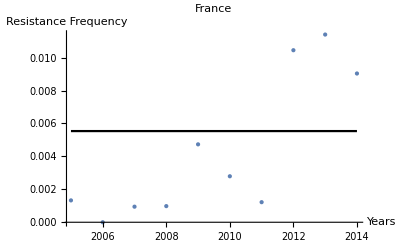

```mathematica
optParams={r0,a,d}/.params
{plot1,plot2} = plotStuff@optParams;
Show[{plot1,plot2},PlotRange->All]
```